```mathematica
Reformat[symb_]:=Row[Riffle[StringSplit[SymbolName[symb],"x"],Style["|",Red, Bold,6]]]
```

```mathematica
MobiusGraph5[key_,allGraphs_]:=Block[{form=allGraphs[key,"colofourrealnull"], vars, blocks=Association[],c,edges,set, found=Association[],realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]]},
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
Graph[vars,edges,VertexLabels->Table[n->Rotate[(Style[Reformat[n],FontFamily->"Consolas",Darker[Green],8]),Pi/6],{n,vars}],ImageSize->600,GraphLayout->"LayeredDigraphEmbedding"]
]
```

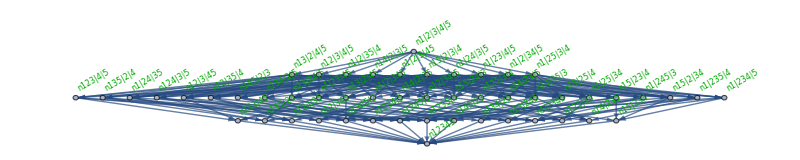
{-Graphics-279-Graphics--n1x2345+n1x234x5+n1x235x4-n1x23x4x5+n1x25x34-n1x25x3x4-n1x2x34x5+n1x2x3x4x5{x^5-3 x^4+3 x^3-x^2,(x-1)^3 x^2,4},-Graphics-280-Graphics--3 n1x2345+n1x234x5+n1x235x4+n1x23x45-n1x23x4x5+n1x245x3+n1x25x34-n1x25x3x4+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5{x^5-4 x^4+6 x^3-3 x^2,(x-1) x^2 (x^2-3 x+3),4},-Graphics-282-Graphics--2 n1x2345+n1x234x5+2 n1x235x4-n1x23x4x5+n1x25x34-n1x25x3x4+n1x2x345-n1x2x34x5-n1x2x35x4+n1x2x3x4x5{x^5-4 x^4+5 x^3-2 x^2,(x-2) (x-1)^2 x^2,0},-Graphics-283-Graphics--4 n1x2345+n1x234x5+2 n1x235x4+n1x23x45-n1x23x4x5+n1x245x3+n1x25x34-n1x25x3x4+2 n1x2x345-n1x2x34x5-n1x2x35x4-n1x2x3x45+n1x2x3x4x5{x^5-5 x^4+8 x^3-4 x^2,(x-2)^2 (x-1) x^2,0},-Graphics-324-Graphics-n1x234x5-n1x23x4x5-n1x24x3x5+n1x2x3x4x5{x^5-2 x^4+x^3,(x-1)^2 x^3,8},-Graphics-325-Graphics--n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x245x3-n1x24x3x5-n1x2x3x45+n1x2x3x4x5{x^5-3 x^4+3 x^3-x^2,(x-1)^3 x^2,4},-Graphics-327-Graphics--n1x2345+n1x234x5+n1x235x4-n1x23x4x5+n1x24x35-n1x24x3x5-n1x2x35x4+n1x2x3x4x5{x^5-3 x^4+3 x^3-x^2,(x-1)^3 x^2,4},-Graphics-328-Graphics--3 n1x2345+n1x234x5+n1x235x4+n1x23x45-n1x23x4x5+n1x245x3+n1x24x35-n1x24x3x5+n1x2x345-n1x2x35x4-n1x2x3x45+n1x2x3x4x5{x^5-4 x^4+6 x^3-3 x^2,(x-1) x^2 (x^2-3 x+3),4},-Graphics-333-Graphics-2 n1x234x5-n1x23x4x5-n1x24x3x5-n1x2x34x5+n1x2x3x4x5{x^5-3 x^4+2 x^3,(x-2) (x-1) x^3,0},-Graphics-334-Graphics--2 n1x2345+2 n1x234x5+n1x23x45-n1x23x4x5+n1x245x3-n1x24x3x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5{x^5-4 x^4+5 x^3-2 x^2,(x-2) (x-1)^2 x^2,0},-Graphics-336-Graphics--2 n1x2345+2 n1x234x5+n1x235x4-n1x23x4x5+n1x24x35-n1x24x3x5+n1x2x345-n1x2x34x5-n1x2x35x4+n1x2x3x4x5{x^5-4 x^4+5 x^3-2 x^2,(x-2) (x-1)^2 x^2,0},-Graphics-337-Graphics--4 n1x2345+2 n1x234x5+n1x235x4+n1x23x45-n1x23x4x5+n1x245x3+n1x24x35-n1x24x3x5+2 n1x2x345-n1x2x34x5-n1x2x35x4-n1x2x3x45+n1x2x3x4x5{x^5-5 x^4+8 x^3-4 x^2,(x-2)^2 (x-1) x^2,0},-Graphics-351-Graphics--n1x2345+n1x234x5+n1x235x4-n1x23x4x5+n1x245x3-n1x24x3x5-n1x25x3x4+n1x2x3x4x5{x^5-3 x^4+3 x^3-x^2,(x-1)^3 x^2,4},-Graphics-352-Graphics--2 n1x2345+n1x234x5+n1x235x4+n1x23x45-n1x23x4x5+2 n1x245x3-n1x24x3x5-n1x25x3x4-n1x2x3x45+n1x2x3x4x5{x^5-4 x^4+5 x^3-2 x^2,(x-2) (x-1)^2 x^2,0},-Graphics-354-Graphics--2 n1x2345+n1x234x5+2 n1x235x4-n1x23x4x5+n1x245x3+n1x24x35-n1x24x3x5-n1x25x3x4-n1x2x35x4+n1x2x3x4x5{x^5-4 x^4+5 x^3-2 x^2,(x-2) (x-1)^2 x^2,0},-Graphics-355-Graphics--4 n1x2345+n1x234x5+2 n1x235x4+n1x23x45-n1x23x4x5+2 n1x245x3+n1x24x35-n1x24x3x5-n1x25x3x4+n1x2x345-n1x2x35x4-n1x2x3x45+n1x2x3x4x5{x^5-5 x^4+8 x^3-4 x^2,(x-2)^2 (x-1) x^2,0},-Graphics-360-Graphics--2 n1x2345+2 n1x234x5+n1x235x4-n1x23x4x5+n1x245x3-n1x24x3x5+n1x25x34-n1x25x3x4-n1x2x34x5+n1x2x3x4x5{x^5-4 x^4+5 x^3-2 x^2,(x-2) (x-1)^2 x^2,0},-Graphics-361-Graphics--4 n1x2345+2 n1x234x5+n1x235x4+n1x23x45-n1x23x4x5+2 n1x245x3-n1x24x3x5+n1x25x34-n1x25x3x4+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5{x^5-5 x^4+8 x^3-4 x^2,(x-2)^2 (x-1) x^2,0},-Graphics-363-Graphics--4 n1x2345+2 n1x234x5+2 n1x235x4-n1x23x4x5+n1x245x3+n1x24x35-n1x24x3x5+n1x25x34-n1x25x3x4+n1x2x345-n1x2x34x5-n1x2x35x4+n1x2x3x4x5{x^5-5 x^4+8 x^3-4 x^2,(x-2)^2 (x-1) x^2,0},-Graphics-364-Graphics--6 n1x2345+2 n1x234x5+2 n1x235x4+n1x23x45-n1x23x4x5+2 n1x245x3+n1x24x35-n1x24x3x5+n1x25x34-n1x25x3x4+2 n1x2x345-n1x2x34x5-n1x2x35x4-n1x2x3x45+n1x2x3x4x5{x^5-6 x^4+11 x^3-6 x^2,(x-3) (x-2) (x-1) x^2,0}}

```mathematica
With[
{all= MobiusGraph5[k5Key,allGraphs5]},
 Table[
With[
{g=MobiusGraph5[k,allGraphs5], gr=allGraphs5[k,"graph"]},
Framed[
Labeled[
Row[{
Labeled[Graph[gr,ImageSize->{40,40}],Style[k,Bold,12, Underlined,Red]],
Graph[all,
GraphHighlight->Join[VertexList[g],EdgeList[g]],
GraphHighlightStyle->"Thick",
ImageSize->800
]
}],
{Style[StandardForm[allGraphs5[k,"colofourrealnull"]],Darker[Green],8],
{Style[TraditionalForm[ ChromaticPolynomial[gr,x]],Blue],Style[TraditionalForm[ ChromaticPolynomial[gr,x]//Factor],Red],Style[ChromaticPolynomial[gr,2],Blue]}},
{Top,Bottom}
]
]
]
,{k,Take[Select[Sort[Keys[allGraphs4]],VertexCount[allGraphs5[#,"graph"]]==5&],-20]}
]
]
```